```mathematica
Clear["Global`*"];
```

#### Benefit function component –– Fighting ability

Assume that the fighting ability  of a group increase linearly with the number of males and females

Males have higher fighting ability than females

The baseline fighting ability is a group of 2 females and 1 male

As fighting ability of a group increases, its benefit has diminishing returns that follow an increasing function a(1-ⅇ^(-(p-p0)/b))

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

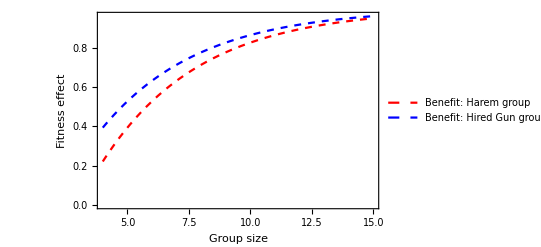

```mathematica
pb=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed}},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

#### Cost function component –– relatedness

```mathematica
data={{2,0.48},{3,0.26},{3,0.36},{4, 0.18},{5,0.24},{5,0.18},{8,0.02},{8,0.14},{12,0.15}, {13, 0.05}, {14, 0.08},{15,0.04},{23,0.02},{25,0.03},{40,0.03},{54, -0.02}, {60, 0.01}};
```

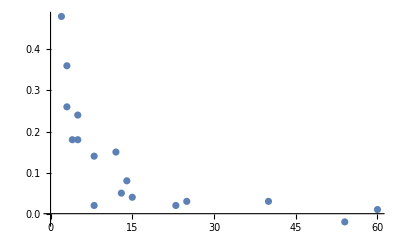

```mathematica
ListPlot[data]
```

```mathematica
mod=c[1] Exp[-c[2] (x)]+c[3];
```

```mathematica
nmf=NonlinearModelFit[data,mod,{Array[c,3],{0.5,0.05,0.}}ᵀ,x]
```

FittedModel[0.0371351+0.819885 ⅇ^(-0.346828 x)]

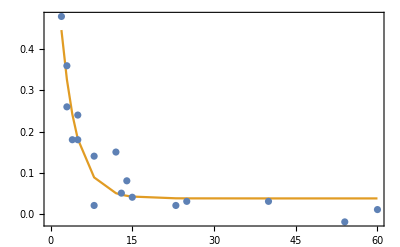

```mathematica
ListPlot[Evaluate[{data,{data[[All,1]],Map[nmf[#]&,data[[All,1]]]}ᵀ}],Joined->{False,True},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],ImageSize->400]
```

```mathematica
r[x_]:=0.82 ⅇ^(-0.35x)+0.037;
```

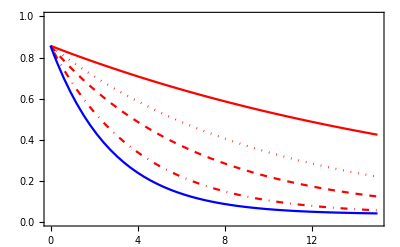

```mathematica
Plot[{0.82 ⅇ^(-0.05x)+0.037,0.82 ⅇ^(-0.1x)+0.037,0.82 ⅇ^(-0.15x)+0.037,0.82 ⅇ^(-0.25x)+0.037,0.82 ⅇ^(-0.35x)+0.037},{x,0,15},PlotRange->{0,1},PlotStyle->{Red,{Red, Dotted},{Red, Dashed},{Red, DotDashed},Blue},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],ImageSize->400]
```

```mathematica
Solve[D[ ⅇ^(-b x)-ⅇ^(-0.35x),x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.667429}}

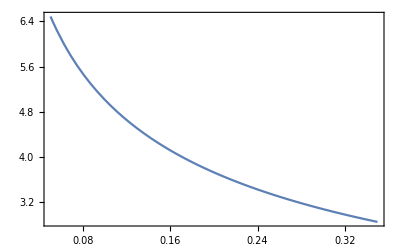

```mathematica
Plot[Log[0.35/β]/(0.35-β),{β,0.05,0.35},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],ImageSize->400]
```

#### Cost function

```mathematica
rHarem[x_]:=0.82 ⅇ^(-0.1x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

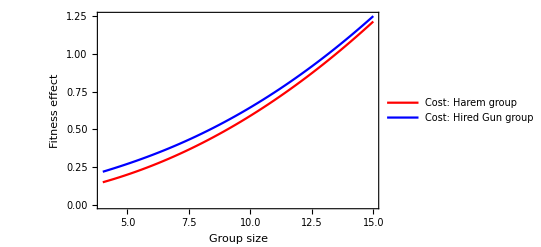

```mathematica
pc=Plot[{kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Cost: Harem group","Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

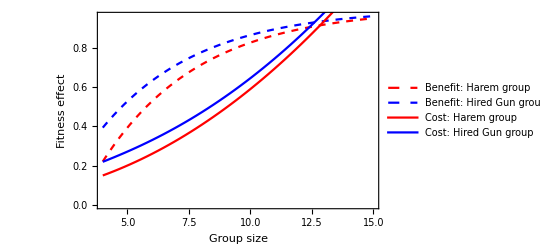

```mathematica
Show[{pb,pc}]
```

#### Difference between benefit and cost

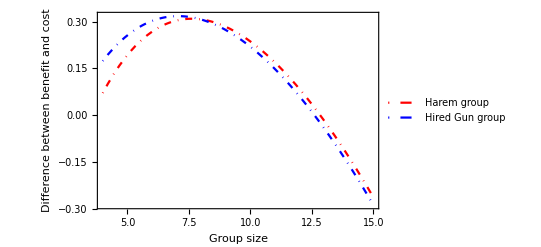

```mathematica
Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{DotDashed,Red},{DotDashed,Blue}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Difference between benefit and cost"}]
```

### Varying Pm

#### Scenario-1: Pm=2

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-0.1x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

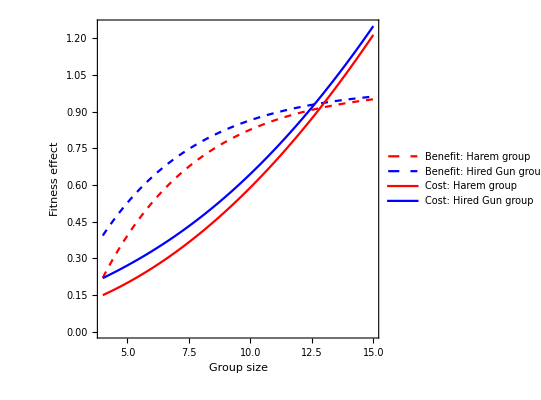

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},AspectRatio->1,PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

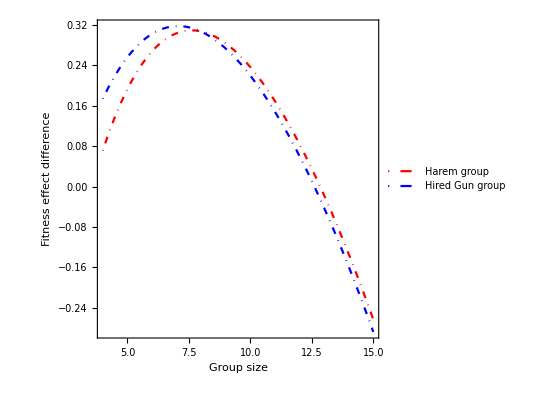

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},AspectRatio->1,PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-2: Pm=1.1

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=1.1;P0=2Pf+Pm;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-0.1x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

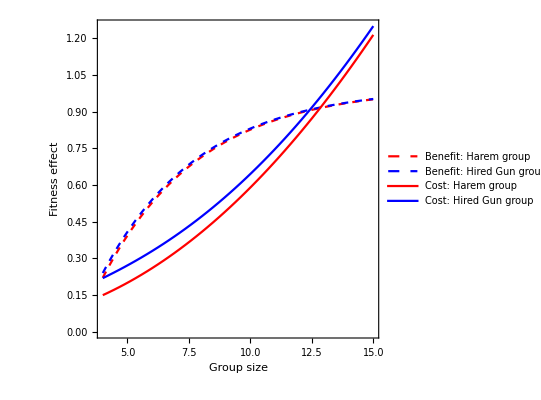

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},AspectRatio->1,PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

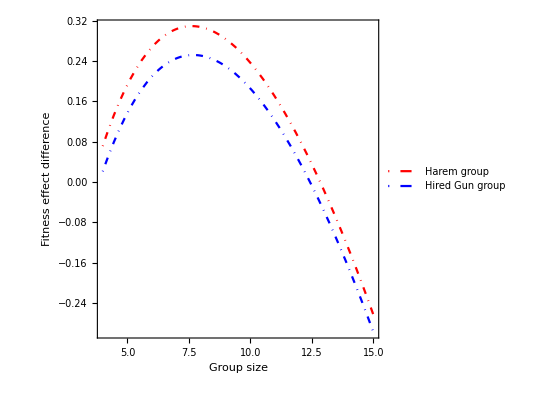

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},AspectRatio->1,PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-2: Pm=5

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=5;P0=2Pf+Pm;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-0.1x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

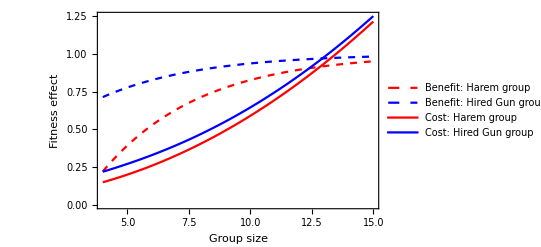

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

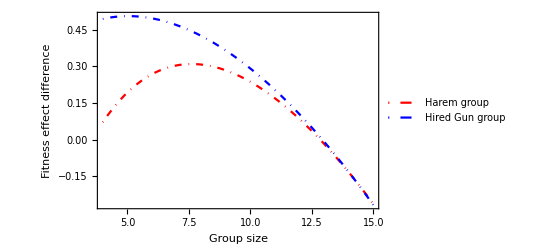

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

### Varying the shape of relatedness function of the harem group

#### Scenario-1: β=0.1

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

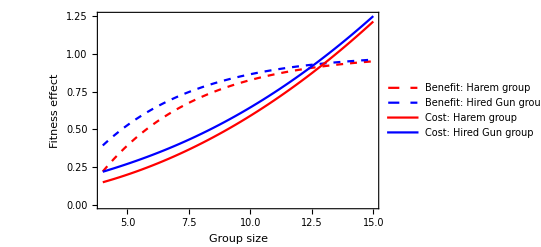

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

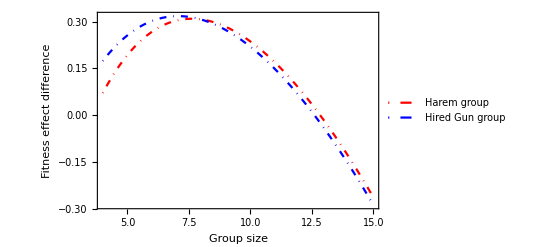

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-2: β=0.05

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.05;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

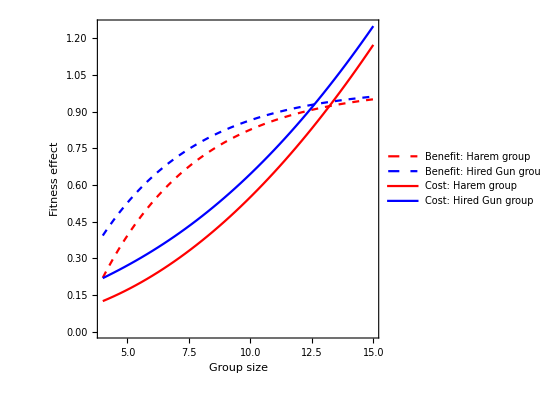

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},AspectRatio->1,PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

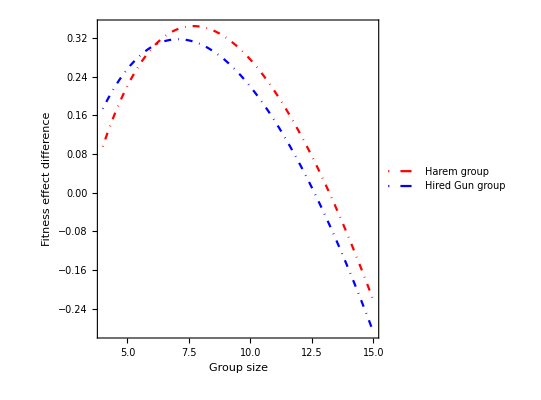

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},AspectRatio->1,PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-3: β=0.2

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.2;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

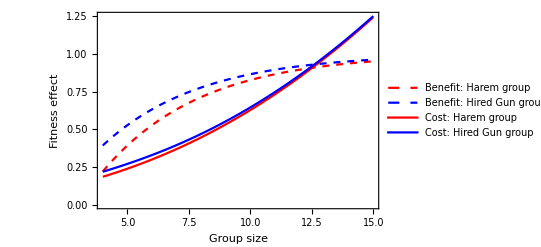

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

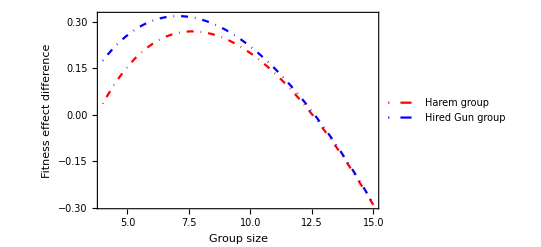

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

### Changing the weight of coordination cost

#### Scenario-1: kc=0.01

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

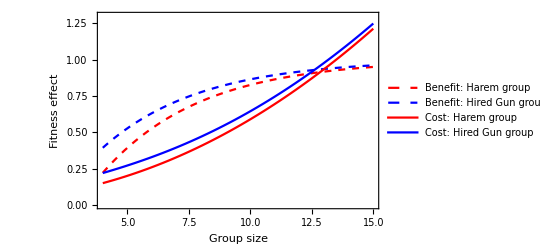

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotRange->{0,1.3},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

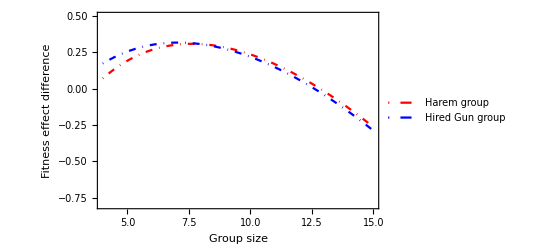

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotRange->{-0.8,0.5},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-2: kc=0.015

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.015;kr=0.2;
```

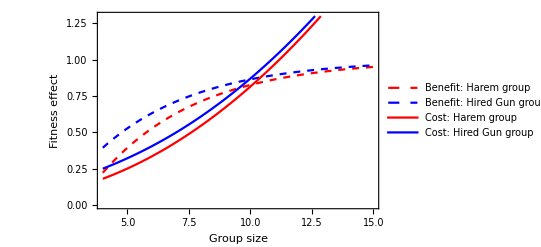

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotRange->{0,1.3},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

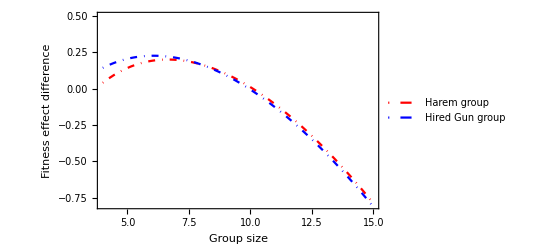

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotRange->{-0.8,0.5},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-2: kc=0.005

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.005;kr=0.2;
```

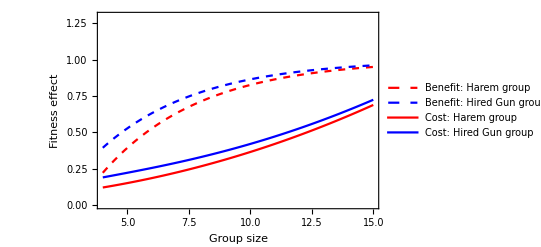

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotRange->{0,1.3},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

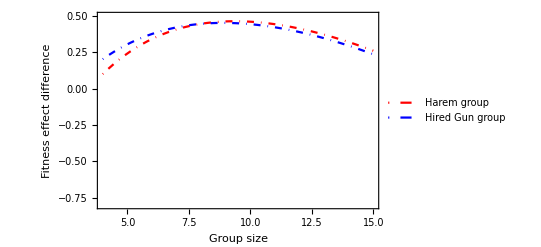

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotRange->{-0.8,0.5},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

### Changing the weight of relatedness cost

#### Scenario-1: kr=0.2

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.2;
```

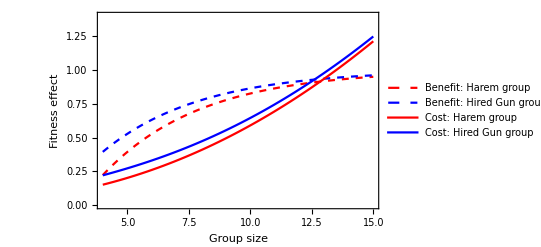

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotRange->{0,1.4},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

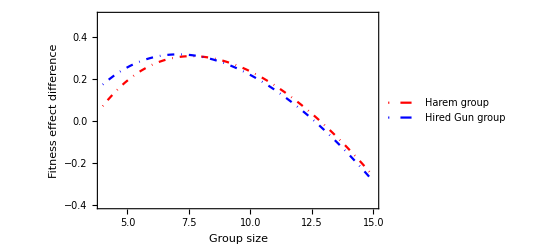

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotRange->{-0.4,0.5},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-2: kr=0.1

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.1;
```

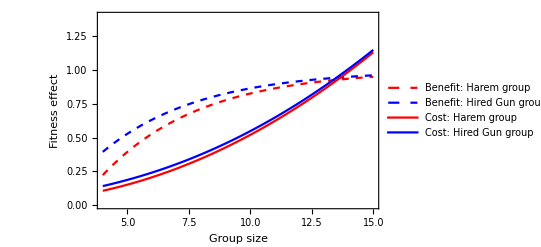

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotRange->{0,1.4},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

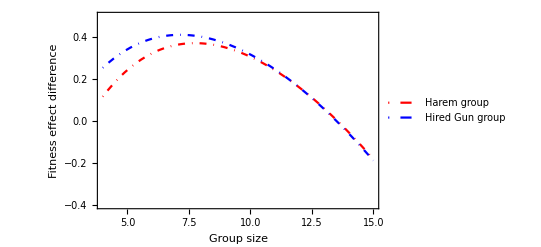

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotRange->{-0.4,0.5},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```

#### Scenario-3: kr=0.3

```mathematica
Clear["Global`*"];
```

```mathematica
a=1;b=4;Pf=1; Pm=2;P0=2Pf+Pm;
```

```mathematica
β=0.1;
```

```mathematica
rHarem[x_]:=0.82 ⅇ^(-β x);
```

```mathematica
rHG[x_]:=0.82 ⅇ^(-0.35x);
```

```mathematica
kc=0.01;kr=0.3;
```

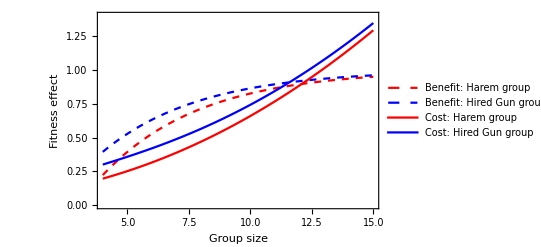

```mathematica
pbc=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b)),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b)),kc(x(x-1))/2+kr(1-rHarem[x]),kc(x(x-1))/2+kr(1-rHG[x])},{x,4,15},PlotRange->{0,1.4},PlotStyle->{{Red,Dashed},{Blue, Dashed},Red,Blue},AxesOrigin->{4,0},PlotLegends->{"Benefit: Harem group","Benefit: Hired Gun group","Cost: Harem group", "Cost: Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect"}]
```

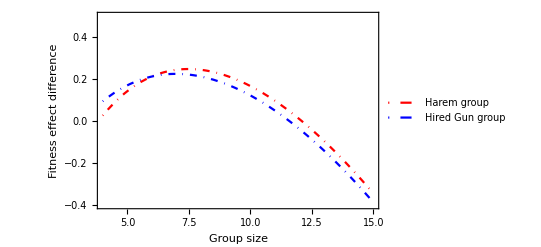

```mathematica
pdiff=Plot[{a(1-ⅇ^(-((x-1)Pf+Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHarem[x])),a(1-ⅇ^(-((x-2)Pf+2Pm-P0)/b))-(kc(x(x-1))/2+kr(1-rHG[x]))},{x,4,15},PlotRange->{-0.4,0.5},PlotStyle->{{Red,DotDashed},{Blue, DotDashed}},AxesOrigin->{4,0},PlotLegends->{"Harem group","Hired Gun group"},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Helvetica"],FrameLabel->{"Group size","Fitness effect difference"}]
```